=== 步骤1：DSolve求解得到的x(t)和y(t)符号解 ===

x(t) = ((1.-1. ⅇ^(-(b t)/m)) m v0 Cos[θ0])/b

y(t) = (m ((9.8-9.8 ⅇ^(-(1. b t)/m)) m-9.8 b t+b (1.-1. ⅇ^(-(1. b t)/m)) v0 Sin[θ0]))/b^2

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

=== 步骤2：Solve消去t后得到的轨道方程y=f(x) ===

y = ConditionalExpression[-(9.8 m^2 Log[(m v0 Cos[θ0])/(-1. b x+m v0 Cos[θ0])])/b^2+(9.8 m x Sec[θ0])/(b v0)+1. x Tan[θ0], ]

=== 步骤3：轨迹对比图 ===

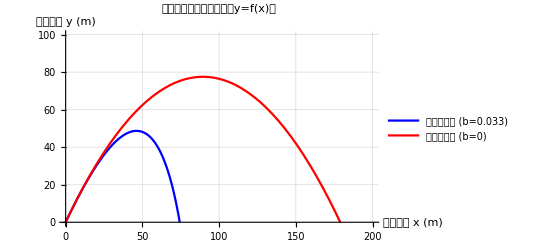

```mathematica
Clear["Global`*"]; g=9.8;
eqns={m x''[t]==-b x'[t],m y''[t]==-m g-b y'[t] };

ic={x[0]==0,y[0]==0,x'[0]==v0 Cos[θ0],y'[0]==v0 Sin[θ0] };
sol=DSolve[{eqns,ic},{x[t],y[t]},t][[1]];x[t_]=x[t]/. sol;y[t_]=y[t]/. sol;

Print["=== 步骤1：DSolve求解得到的x(t)和y(t)符号解 ==="];
Print["x(t) = ",Simplify[x[t]]];
Print["y(t) = ",Simplify[y[t]]];

tFromX=Solve[x[t]==x,t,Reals][[1,1,2]];orbitEquation=Simplify[y[t]/. t->tFromX];

Print["\n=== 步骤2：Solve消去t后得到的轨道方程y=f(x) ==="];
Print["y = ",orbitEquation];


paramsWithDrag={m->0.14,v0->45,θ0->60 Degree,b->0.033};
yWithDrag[x_]=Simplify[orbitEquation/. paramsWithDrag];
paramsNoDrag={v0->45,θ0->60 Degree};
v0Val=v0/. paramsNoDrag;
θ0Val=θ0/. paramsNoDrag;
yNoDrag[x_]=x Tan[θ0Val]-(g x^2)/(2 v0Val^2 Cos[θ0Val]^2);
Print["\n=== 步骤3：轨迹对比图 ==="];
Plot[{yWithDrag[x],yNoDrag[x]},{x,0,200},PlotLegends->{"有空气阻力 (b=0.033)","无空气阻力 (b=0)"},AxesLabel->{"水平位移 x (m)","竖直位移 y (m)"},PlotLabel->"抛体运动轨道方程对比（y=f(x)）",PlotStyle->{Blue,Red},GridLines->Automatic,PlotRange->{{0,200},{0,100}},BaseStyle->{FontSize->12}]
```